```mathematica
a = -1;
b = 3;
n = 9;
h = (b-a)/(n-1);
z = (a - h);
X =Table[z += h, n];
i = 1;
f[x_]:=-Sin[4-x^2];
Y = Table[f[X[[i]]], n];
For[i = 1, i ≤ n, i++, Y[[i]] = f[X[[i]]]];
f[x_]:=-Sin[4-x^2];
raz2[x1_,x2_]:=(f[x2]-f[x1])/(x2-x1);
raz3[x1_,x2_,x3_]:=(raz2[x2,x3]-raz2[x1,x2])/(x3-x1);
raz4[x1_,x2_,x3_,x4_]:=(raz3[x2,x3,x4]-raz3[x1,x2,x3])/(x4-x1);
raz5[x1_,x2_,x3_,x4_,x5_]:=(raz4[x2,x3,x4,x5]-raz4[x1,x2,x3,x4])/(x5-x1);
raz6[x1_,x2_,x3_,x4_,x5_,x6_]:=(raz5[x2,x3,x4,x5,x6]-raz5[x1,x2,x3,x4,x5])/(x6-x1);
raz7[x1_,x2_,x3_,x4_,x5_,x6_,x7_]:=(raz6[x2,x3,x4,x5,x6,x7]-raz6[x1,x2,x3,x4,x5,x6])/(x7-x1);
raz8[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_]:=(raz7[x2,x3,x4,x5,x6,x7,x8]-raz7[x1,x2,x3,x4,x5,x6,x7])/(x8-x1);
raz9[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_]:=(raz8[x2,x3,x4,x5,x6,x7,x8,x9]-raz8[x1,x2,x3,x4,x5,x6,x7,x8])/(x9-x1);
Raz=Table[0,n];
Raz[[1]]=f[X[[1]]];
Raz[[2]]=raz2[X[[1]],X[[2]]];
Raz[[3]]=raz3[X[[1]],X[[2]],X[[3]]];
Raz[[4]]=raz4[X[[1]],X[[2]],X[[3]],X[[4]]];
Raz[[5]]=raz5[X[[1]],X[[2]],X[[3]],X[[4]],X[[5]]];
Raz[[6]]=raz6[X[[1]],X[[2]],X[[3]],X[[4]],X[[5]],X[[6]]];
Raz[[7]]=raz7[X[[1]],X[[2]],X[[3]],X[[4]],X[[5]],X[[6]],X[[7]]];
Raz[[8]]=raz8[X[[1]],X[[2]],X[[3]],X[[4]],X[[5]],X[[6]],X[[7]],X[[8]]];
Raz[[9]]=raz9[X[[1]],X[[2]],X[[3]],X[[4]],X[[5]],X[[6]],X[[7]],X[[8]],X[[9]]];
F=0;
For[i=1,i≤n,i++,
{
If[i==0,S=0,S=Raz[[i]]];
For[j=1,j<i,j++,S*=(x-X[[j]])];
F+=S;
}];
N[Collect[F,x]]
```

0.756802-0.342169 x-0.117024 x^2+1.45396 x^3-3.03165 x^4-0.0842725 x^5+2.10783 x^6-1.02752 x^7+0.142925 x^8

```mathematica
Newt[x_]:=-Sin[3]+2(1+x)(Sin[3]-Sin[15/4])+(1/2+x)(1+x)(-2(Sin[3]-Sin[15/4])+2(Sin[15/4]-Sin[4]))+2/3x(1/2+x)(1+x)(2(Sin[3]-Sin[15/4])-4(Sin[15/4]-Sin[4])+2(-Sin[15/4]+Sin[4]))+1/2(-(1/2)+x)x(1/2+x)(1+x)(2/3(2(-Sin[3]+Sin[15/4])+2(Sin[15/4]-Sin[4])-4(-Sin[15/4]+Sin[4]))-2/3(2(Sin[3]-Sin[15/4])-4(Sin[15/4]-Sin[4])+2(-Sin[15/4]+Sin[4])))+2/5(-1+x)(-(1/2)+x)x(1/2+x)(1+x)(1/2(-(2/3)(2(-Sin[3]+Sin[15/4])+2(Sin[15/4]-Sin[4])-4(-Sin[15/4]+Sin[4]))+2/3(2(-Sin[7/4]+Sin[3])-4(-Sin[3]+Sin[15/4])+2(-Sin[15/4]+Sin[4])))+1/2(-(2/3)(2(-Sin[3]+Sin[15/4])+2(Sin[15/4]-Sin[4])-4(-Sin[15/4]+Sin[4]))+2/3(2(Sin[3]-Sin[15/4])-4(Sin[15/4]-Sin[4])+2(-Sin[15/4]+Sin[4]))))+1/3(-(3/2)+x)(-1+x)(-(1/2)+x)x(1/2+x)(1+x)(2/5(1/2(2/3(2Sin[7/4]-4(-Sin[7/4]+Sin[3])+2(-Sin[3]+Sin[15/4]))-2/3(2(-Sin[7/4]+Sin[3])-4(-Sin[3]+Sin[15/4])+2(-Sin[15/4]+Sin[4])))+1/2(2/3(2(-Sin[3]+Sin[15/4])+2(Sin[15/4]-Sin[4])-4(-Sin[15/4]+Sin[4]))-2/3(2(-Sin[7/4]+Sin[3])-4(-Sin[3]+Sin[15/4])+2(-Sin[15/4]+Sin[4]))))-2/5(1/2(-(2/3)(2(-Sin[3]+Sin[15/4])+2(Sin[15/4]-Sin[4])-4(-Sin[15/4]+Sin[4]))+2/3(2(-Sin[7/4]+Sin[3])-4(-Sin[3]+Sin[15/4])+2(-Sin[15/4]+Sin[4])))+1/2(-(2/3)(2(-Sin[3]+Sin[15/4])+2(Sin[15/4]-Sin[4])-4(-Sin[15/4]+Sin[4]))+2/3(2(Sin[3]-Sin[15/4])-4(Sin[15/4]-Sin[4])+2(-Sin[15/4]+Sin[4])))))+2/7(-2+x)(-(3/2)+x)(-1+x)(-(1/2)+x)x(1/2+x)(1+x)(1/3(-(2/5)(1/2(2/3(2Sin[7/4]-4(-Sin[7/4]+Sin[3])+2(-Sin[3]+Sin[15/4]))-2/3(2(-Sin[7/4]+Sin[3])-4(-Sin[3]+Sin[15/4])+2(-Sin[15/4]+Sin[4])))+1/2(2/3(2(-Sin[3]+Sin[15/4])+2(Sin[15/4]-Sin[4])-4(-Sin[15/4]+Sin[4]))-2/3(2(-Sin[7/4]+Sin[3])-4(-Sin[3]+Sin[15/4])+2(-Sin[15/4]+Sin[4]))))+2/5(1/2(2/3(-4Sin[7/4]+2Sin[9/4]+2(-Sin[7/4]+Sin[3]))-2/3(2Sin[7/4]-4(-Sin[7/4]+Sin[3])+2(-Sin[3]+Sin[15/4])))+1/2(-(2/3)(2Sin[7/4]-4(-Sin[7/4]+Sin[3])+2(-Sin[3]+Sin[15/4]))+2/3(2(-Sin[7/4]+Sin[3])-4(-Sin[3]+Sin[15/4])+2(-Sin[15/4]+Sin[4])))))+1/3(-(2/5)(1/2(2/3(2Sin[7/4]-4(-Sin[7/4]+Sin[3])+2(-Sin[3]+Sin[15/4]))-2/3(2(-Sin[7/4]+Sin[3])-4(-Sin[3]+Sin[15/4])+2(-Sin[15/4]+Sin[4])))+1/2(2/3(2(-Sin[3]+Sin[15/4])+2(Sin[15/4]-Sin[4])-4(-Sin[15/4]+Sin[4]))-2/3(2(-Sin[7/4]+Sin[3])-4(-Sin[3]+Sin[15/4])+2(-Sin[15/4]+Sin[4]))))+2/5(1/2(-(2/3)(2(-Sin[3]+Sin[15/4])+2(Sin[15/4]-Sin[4])-4(-Sin[15/4]+Sin[4]))+2/3(2(-Sin[7/4]+Sin[3])-4(-Sin[3]+Sin[15/4])+2(-Sin[15/4]+Sin[4])))+1/2(-(2/3)(2(-Sin[3]+Sin[15/4])+2(Sin[15/4]-Sin[4])-4(-Sin[15/4]+Sin[4]))+2/3(2(Sin[3]-Sin[15/4])-4(Sin[15/4]-Sin[4])+2(-Sin[15/4]+Sin[4]))))))+1/4(-(5/2)+x)(-2+x)(-(3/2)+x)(-1+x)(-(1/2)+x)x(1/2+x)(1+x)(-(2/7)(1/3(-(2/5)(1/2(2/3(2Sin[7/4]-4(-Sin[7/4]+Sin[3])+2(-Sin[3]+Sin[15/4]))-2/3(2(-Sin[7/4]+Sin[3])-4(-Sin[3]+Sin[15/4])+2(-Sin[15/4]+Sin[4])))+1/2(2/3(2(-Sin[3]+Sin[15/4])+2(Sin[15/4]-Sin[4])-4(-Sin[15/4]+Sin[4]))-2/3(2(-Sin[7/4]+Sin[3])-4(-Sin[3]+Sin[15/4])+2(-Sin[15/4]+Sin[4]))))+2/5(1/2(2/3(-4Sin[7/4]+2Sin[9/4]+2(-Sin[7/4]+Sin[3]))-2/3(2Sin[7/4]-4(-Sin[7/4]+Sin[3])+2(-Sin[3]+Sin[15/4])))+1/2(-(2/3)(2Sin[7/4]-4(-Sin[7/4]+Sin[3])+2(-Sin[3]+Sin[15/4]))+2/3(2(-Sin[7/4]+Sin[3])-4(-Sin[3]+Sin[15/4])+2(-Sin[15/4]+Sin[4])))))+1/3(-(2/5)(1/2(2/3(2Sin[7/4]-4(-Sin[7/4]+Sin[3])+2(-Sin[3]+Sin[15/4]))-2/3(2(-Sin[7/4]+Sin[3])-4(-Sin[3]+Sin[15/4])+2(-Sin[15/4]+Sin[4])))+1/2(2/3(2(-Sin[3]+Sin[15/4])+2(Sin[15/4]-Sin[4])-4(-Sin[15/4]+Sin[4]))-2/3(2(-Sin[7/4]+Sin[3])-4(-Sin[3]+Sin[15/4])+2(-Sin[15/4]+Sin[4]))))+2/5(1/2(-(2/3)(2(-Sin[3]+Sin[15/4])+2(Sin[15/4]-Sin[4])-4(-Sin[15/4]+Sin[4]))+2/3(2(-Sin[7/4]+Sin[3])-4(-Sin[3]+Sin[15/4])+2(-Sin[15/4]+Sin[4])))+1/2(-(2/3)(2(-Sin[3]+Sin[15/4])+2(Sin[15/4]-Sin[4])-4(-Sin[15/4]+Sin[4]))+2/3(2(Sin[3]-Sin[15/4])-4(Sin[15/4]-Sin[4])+2(-Sin[15/4]+Sin[4]))))))+2/7(1/3(2/5(1/2(2/3(2Sin[7/4]-4(-Sin[7/4]+Sin[3])+2(-Sin[3]+Sin[15/4]))-2/3(2(-Sin[7/4]+Sin[3])-4(-Sin[3]+Sin[15/4])+2(-Sin[15/4]+Sin[4])))+1/2(2/3(2(-Sin[3]+Sin[15/4])+2(Sin[15/4]-Sin[4])-4(-Sin[15/4]+Sin[4]))-2/3(2(-Sin[7/4]+Sin[3])-4(-Sin[3]+Sin[15/4])+2(-Sin[15/4]+Sin[4]))))-2/5(1/2(2/3(-4Sin[7/4]+2Sin[9/4]+2(-Sin[7/4]+Sin[3]))-2/3(2Sin[7/4]-4(-Sin[7/4]+Sin[3])+2(-Sin[3]+Sin[15/4])))+1/2(-(2/3)(2Sin[7/4]-4(-Sin[7/4]+Sin[3])+2(-Sin[3]+Sin[15/4]))+2/3(2(-Sin[7/4]+Sin[3])-4(-Sin[3]+Sin[15/4])+2(-Sin[15/4]+Sin[4])))))+1/3(-(2/5)(1/2(2/3(-4Sin[7/4]+2Sin[9/4]+2(-Sin[7/4]+Sin[3]))-2/3(2Sin[7/4]-4(-Sin[7/4]+Sin[3])+2(-Sin[3]+Sin[15/4])))+1/2(-(2/3)(2Sin[7/4]-4(-Sin[7/4]+Sin[3])+2(-Sin[3]+Sin[15/4]))+2/3(2(-Sin[7/4]+Sin[3])-4(-Sin[3]+Sin[15/4])+2(-Sin[15/4]+Sin[4]))))+2/5(1/2(-(2/3)(-4Sin[7/4]+2Sin[9/4]+2(-Sin[7/4]+Sin[3]))+2/3(2Sin[7/4]-4(-Sin[7/4]+Sin[3])+2(-Sin[3]+Sin[15/4])))+1/2(-(2/3)(-4Sin[7/4]+2Sin[9/4]+2(-Sin[7/4]+Sin[3]))+2/3(2Sin[7/4]-4Sin[9/4]+2(-Sin[9/4]+Sin[5])))))));
Y2=Table[0,n];
For[i=1,i≤n,i++,Y2[[i]]=Newt[X[[i]]]];
```

{{-1,-Sin[3]},{-1/2,-Sin[15/4]},{0,-Sin[4]},{1/2,-Sin[15/4]},{1,-Sin[3]},{3/2,-Sin[7/4]},{2,0},{5/2,Sin[9/4]},{3,Sin[5]}}

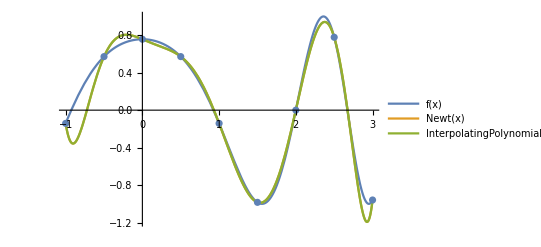

```mathematica
Data=Transpose[{X,Y}]
Show[Plot[{f[x],Newt[x],InterpolatingPolynomial[{{-1,-Sin[3]},{-1/2,-Sin[15/4]},{0,-Sin[4]},{1/2,-Sin[15/4]},{1,-Sin[3]},{3/2,-Sin[7/4]},
{2,0},{5/2,Sin[9/4]},{3,Sin[5]}},x]},{x,a,b},PlotLegends->"Expressions"],ListPlot[Data]]
```